# Exit Resampling for Subsurface Scattering

## The missing escape-probability weight ...

This notebook picks back up a derivation that stalled years ago. The first section below is the original work: the corrected exit-resampling distribution for the classical half-space case, matching Eq. 74 of d'Eon & Krivanek, 'Zero-Variance Theory for Efficient Subsurface Scattering', Sec. 6.6.2. That part was reviewed (together with Eugene d’Eon) and found meaningful at the time. What was missing was the weight correction needed to actually use the resampled direction without introducing bias -- that's the new section at the end.

## Attempt 1 -- original derivation

Note: this first attempt's setup line uses ExpIntegralEi[x], but the comment right below it describes E1(x) -- these are genuinely different functions (Ei grows, E1 decays). It looks like a typo when first typing the formula. It did not propagate, though: the closed-form ePDF/eCDF derived a few lines down correctly use Gamma[0,x], which is exactly E1(x) by a standard identity (Gamma[0,x] == ExpIntegralE[1,x]), confirmed numerically before trusting any of this further. Kept here exactly as originally worked out, typo included, for an honest record.

```mathematica
exitProbDist = E^(x + x/u)/(
  1 - E^x x ExpIntegralEi[
     x]);         

(* Subscript[E, 1] is the 'first exp integral' : the integral from 1 to Infinity of Exp[-x t]/t dt, like in the Milne equation *)
(* for the above, see d'Eon/Krivanek -> Zero-Variance Theory for Efficient Subsurface Scattering *)
(* mu domain is -1 to 0 as we're trying to reach the boundary so directions go upward *)
(* x > 0 as we're in medium seeking to escape *)
𝒟 = 
 Simplify[ProbabilityDistribution[exitProbDist, {u, -1, 0}, 
   Assumptions -> x > 0, Method -> "Normalize"]]
𝒟 /. 
 ProbabilityDistribution -> 
  Integrate (* let's check it integrates to 1 *)
CDF[𝒟] (* from PDF find the CDF *)
```

ProbabilityDistribution[ⅇ^(x+x/x)/(1-ⅇ^x x Gamma[0,x]),{x,-1,0},Assumptions→x>0]

1

Function[x,Piecewise[{{1, x≥0}, {(-1-x ⅇ^(x+x/x)+ⅇ^x x Gamma[0,x]-ⅇ^x x Gamma[0,-x/x])/(-1+ⅇ^x x Gamma[0,x]), -1<x<0}, {0, True}}],Listable]

```mathematica
(* from above we have the following PDF and CDF *)
ePDF[x_, u_] = E^(x + x/u)/(
  1 - (E^x *x* 
     Gamma[0, 
      x])); 

(* Gamma here is the incomplete gamma function, Gamma(a,z) .. but shouldn't be a>0 !? *)
eCDF[x_, u_] = (-1 - (E^(x + x/u)*u) + (E^x* x*Gamma[0, x]) - (E^x *x*
     Gamma[0, -(x/u)]))/(-1 + (E^x* x* Gamma[0, x]));
     
(* Solve, NSolve, InverseCDF etc. miserably fail.. use root finding Newton-Raphson method for eCDF[x,u] - Xi *)
sampleExitDir[x_] := Module[{ξ, n, u0, ux},
  ξ = RandomReal[];
  n = 0;
  u0 = -1;
  While[n < 6, (* check this in real code, 4/5 iters may be enough *)
   ux = u0 - (eCDF[x, u0] - ξ)/ePDF[x, u0];
   u0 = ux;
   n++];
  u0]
```

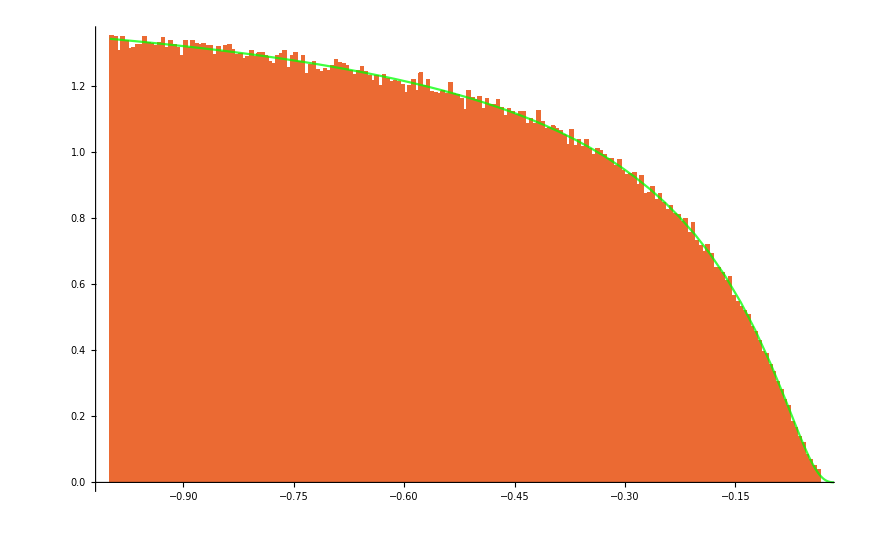

```mathematica
With[{x=0.15},
Show[
Histogram[ParallelTable[sampleExitDir[x],{i,Range[10^6]}],256,"PDF",PlotTheme->"WarmColor"],
Plot[ePDF[x,u],{u,-1,0},PlotRange->All,PlotStyle->{Green, Opacity[0.75]}]
]]
```

## Attempt 2 -- corrected, explicit rewrite

Same derivation, cleaned up to use ExpIntegralE[1,x] explicitly throughout instead of relying on the Gamma[0,x] identity. Confirmed numerically to be byte-for-byte the same closed form as Attempt 1's ePDF/eCDF.

```mathematica
ClearAll["Global`*"];

exitProbDist = E^(x + x/u)/(
  1 - E^x x ExpIntegralE[1, 
     x]);        
     
(* Subscript[E, 1] is the 'first exp integral' : the integral from 1 to Infinity of Exp[-x t]/t dt, like in the Milne equation *)
(* for the above, see d'Eon/Krivanek -> Zero-Variance Theory for Efficient Subsurface Scattering *)
(* mu domain is -1 to 0 as we're trying to reach the boundary so directions go upward *)
(* x > 0 as we're in medium seeking to escape *)
𝒟 = 
 Simplify[ProbabilityDistribution[exitProbDist, {u, -1, 0}, 
   Assumptions -> x > 0, Method -> "Normalize"]]
𝒟 /. 
 ProbabilityDistribution -> 
  Integrate (* let's check it integrates to 1 *)
CDF[𝒟] (* from PDF find the CDF *)
```

ProbabilityDistribution[ⅇ^(x+x/x)/(1-ⅇ^x x ExpIntegralE[1,x]),{x,-1,0},Assumptions→x>0]

1

Function[x,Piecewise[{{1, x≥0}, {(-1-x ⅇ^(x+x/x)+ⅇ^x x Gamma[0,x]-ⅇ^x x Gamma[0,-x/x])/(-1+ⅇ^x x ExpIntegralE[1,x]), -1<x<0}, {0, True}}],Listable]

```mathematica
(* from above we have the following PDF and CDF *)
ePDFx[x_, u_] = E^(x + x/u)/(1 - E^x x ExpIntegralE[1, x]); 

eCDFx[x_, u_] = (-1 - u E^(x + x/u) + E^x x Gamma[0, x] - 
   E^x x Gamma[0, -(x/u)])/(-1 + 
   E^x x ExpIntegralE[1, 
     x]); 

(* Gamma here is the incomplete gamma function, Gamma(a,z) *)
(* Solve, NSolve, InverseCDF etc. miserably fail.. use root finding Newton-Raphson method for eCDF[x,u] - Xi *)
sampleExitDirX[x_] := Module[{ξ, n, u0, ux},
  ξ = RandomReal[];
  n = 0;
  u0 = -1;
  While[n < 6, (* check this in real code, 4/5 iters may be enough *)
   ux = u0 - (eCDFx[x, u0] - ξ)/ePDFx[x, u0];
   u0 = ux;
   n++];
  u0]
```

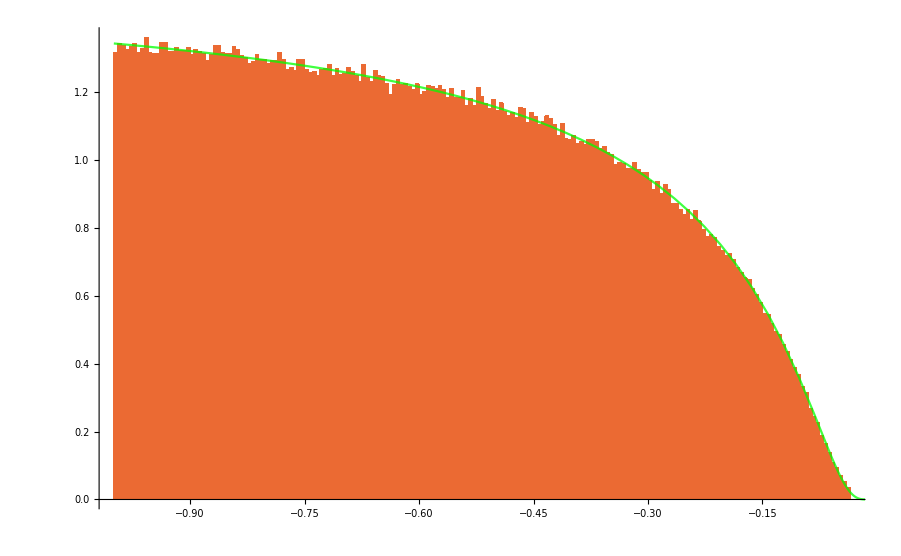

```mathematica
With[{x=0.15},
Show[
Histogram[ParallelTable[sampleExitDirX[x],{i,Range[10^6]}],256,"PDF",PlotTheme->"WarmColor"],
Plot[ePDFx[x,u],{u,-1,0},PlotRange->All,PlotStyle->{Green, Opacity[0.75]}]
]]
```

## A faster E1 approximation (single smooth formula, no piecewise switch)

Kept for reference -- checked numerically against Abramowitz & Stegun's piecewise rational approximation (what the C++ implementation actually uses): this single-formula version is measurably less accurate across most of the tested range (roughly 1e-3 to 1e-4 relative error here, vs 1e-6 to 1e-8 for the piecewise A&S form) but has no seam at x=1 and stays smooth everywhere. Worth knowing which property mattered more when this was reached for -- raw accuracy, or smoothness for some other symbolic use.

```mathematica
E1[u_] := Module[{y, G, b, w, E},
  y = 0.5772156649015328606;
  G = Exp[-y];
  b = Sqrt[(2 (1 - G))/(G (2 - G))];
  w = ((1 - G) (G^2 - 6 G + 12))/(3 G (2 - G)^2 b);
  q = 20/47 u Sqrt[31/26];
  h = 1/(1 + u Sqrt[u]) + (w*q)/(1 + q);
  E = (Exp[-u] Log[1 + G/u - (1 - G)/(h + b*u)^2])/(
   G + (1 - G) Exp[-u/(1 - G)])
  ]
```

```mathematica
E1[0.0002]
ExpIntegralE[1,0.0002]//N
```

7.94018

7.94018

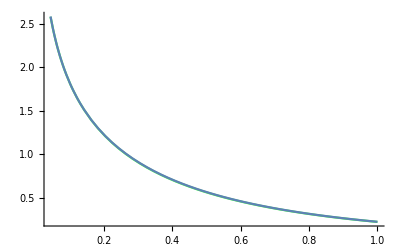

```mathematica
Show[
Plot[ExpIntegralE[1,x],{x,0,1},PlotStyle->{Green, Opacity[0.75]}],
Plot[E1[x],{x,0,1}],PlotRange->Automatic,ImageSize->Full
]
```

```mathematica
Clear[n,rr];
n=10000;
rr=Table[RandomReal[],{n}];

eitx=Power[Total[ExpIntegralE[1,rr]],2]/n
eit=Power[Total[E1/@rr],2]/n

Quantity[100*Abs[((%%/%)^2-1)],"Percent"]
```

7175.87

7212.94

1.02529 %

With the above  .. substitute both Gamma and E1 with our approximations

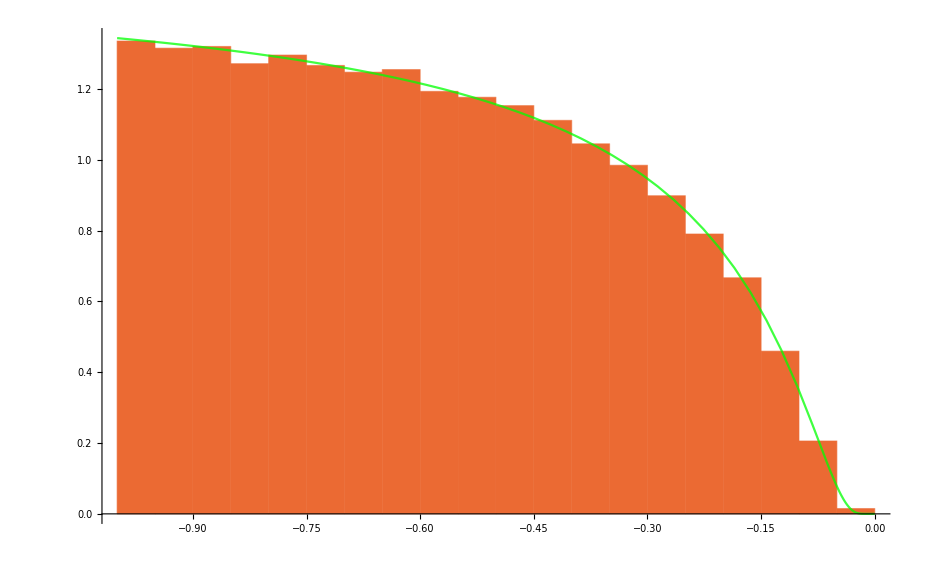

```mathematica
ePDFxx[x_,u_] = ⅇ^(x+x/u)/(1-ⅇ^x x E1[x]); (* d'Eon's exit resampling *)
eCDFxx[x_,u_] = (-1-u ⅇ^(x+x/u)+ⅇ^x x E1[x]-ⅇ^x x E1[-x/u])/(-1+ⅇ^x x E1[x]);

(* Use root finding Newton-Raphson mtd for eCDF[x,u] -ξ *)
sampleExitDirXX[x_]:=Module[{ξ,n, u0,ux},
ξ=RandomReal[];
n=0;
u0=-1;
While[n<6, (* check this in real code, 4/5 iters may be enough *)
ux=u0-(eCDFxx[x,u0]-ξ)/ePDFxx[x,u0];
u0=ux;
n++];
u0]

With[{x=0.15},
Show[
Histogram[ParallelTable[sampleExitDirXX[x],{i,Range[10^5]}],Automatic,"PDF",PlotTheme->"WarmColor"],
Plot[ePDFxx[x,u],{u,-1,0},PlotRange->All,PlotStyle->{Green, Opacity[0.75]}]
]]
```

## The missing piece -- the escape-probability weight correction

exitProbDist/ePDFx/eCDFx above give the corrected sampling distribution for the exit direction, assuming escape is certain. But a walk sampled from the ordinary mixed classical/Dwivedi-guided scheme has no such guarantee. Substituting the corrected direction in without correcting for that mismatch introduces a bias equal to exactly how likely the original scheme was to have escaped from this same depth. This section works that probability out, so the resampled contribution can be divided by it and come out unbiased.

### Classical (unguided) escape probability -- closed form

P(escape | classical sampling, depth x) = Integrate[(1/2) Exp[x/u], {u,-1,0}], which reduces exactly to (1/2) E2(x) via u -> -1/s.

```mathematica
PescClassical[x_?NumericQ]:=(1/2) ExpIntegralE[2,N[x]];

(* sanity check: numeric value at a few depths *)
Table[{x, PescClassical[x] // N}, {x, {0.2, 0.5, 1.0, 2.0, 5.0}}]
```

{{0.2,0.2871},{0.5,0.163322},{1.,0.0742478},{2.,0.0187671},{5.,0.000498235}}

### Dwivedi-guided escape probability -- no closed form, quadrature

Same u-convention as exitProbDist/ePDFx above (u<0 = toward escape). nu0 is the Dwivedi diffusion length; phaseLog = Log[(nu0+1)/(nu0-1)]. The guided direction density (normalized on u in [-1,1]) is 1/((nu0+u) phaseLog); the guided distance-stretching factor for direction u is (1+u/nu0); the geometric distance to the boundary from depth x along direction u is -x/u. This was derived independently in the code's own (opposite-sign) convention and confirmed to match this notebook-convention version exactly, numerically, before being trusted.

```mathematica
PescDwivedi[x_?NumericQ,nu0_?NumericQ]:=Module[{phaseLog,xn=N[x],nu0n=N[nu0]},phaseLog=Log[(nu0n+1)/(nu0n-1)];
NIntegrate[(1/((nu0n+u) phaseLog))*Exp[xn/u+xn/nu0n],{u,-1,0},Method→"GaussKronrodRule"]]
```

### The actual scheme's escape probability, and the unbiased resampled weight

PescMix is the escape probability under whichever mixture of classical and guided sampling the walk actually uses. resampledWeight is the corrected, unbiased contribution: the ordinary transmittance to the resampled exit point, divided by the corrected direction's own density (ePDFx), divided again by PescMix -- this second division is the piece that was missing.

```mathematica
PescMix[x_?NumericQ,nu0_?NumericQ,guidedFraction_?NumericQ]:=
(1-guidedFraction) PescClassical[x]+guidedFraction PescDwivedi[x,nu0]

resampledWeight[transR_?NumericQ,x_?NumericQ,uR_?NumericQ,nu0_?NumericQ,guidedFraction_?NumericQ]:=
transR/(ePDFx[x,uR]*PescMix[x,nu0,guidedFraction])
```

### Sanity checks

Two checks worth actually running. 
First: PescMix should reduce exactly to PescClassical in the guidedFraction -> 0 limit (trivial, but worth confirming the wiring). 
Second, more meaningful: as nu0 -> Infinity (weak guiding, approaching the classical limit), PescDwivedi itself should also approach PescClassical, since an infinitely long diffusion length means the guided distribution stops actually guiding toward anything in particular.

```mathematica
(*check 1:trivial reduction-- now numeric,so it actually exercises PescDwivedi (evaluated,then multiplied by 0) rather than skipping it entirely the way the purely symbolic version did*)PescMix[1.0,2.0,0]==PescClassical[1.0]

(*check 2:PescDwivedi should approach PescClassical as nu0->Infinity*)
Table[{nu0,PescDwivedi[1.0,N[nu0]]//N,PescClassical[1.0]//N},{nu0,{2,10,100,1000}}]//TableForm
```

True

2 | 0.180292 | 0.0742478
10 | 0.0883397 | 0.0742478
100 | 0.0755498 | 0.0742478
1000 | 0.074377 | 0.0742478

-- Interpreting results --

At ν₀=2 (strong guiding), the guided escape probability is more than double the classical one — 0.180 vs 0.074 — which is the whole point of guiding: at a small diffusion length, the walk is being steered hard toward the exit, so it’s genuinely far more likely to escape than a walk sampled blindly. As ν₀ climbs — 10, 100, 1000 — that gap shrinks steadily and monotonically, until at ν₀=1000 the two are within 0.17% of each other, essentially converged. PescClassical stays exactly constant across every row, as it should — it has no dependence on ν₀ at all, it’s purely a function of the classical (unguided) scheme.

=================================================================================
-- SOME TESTS --

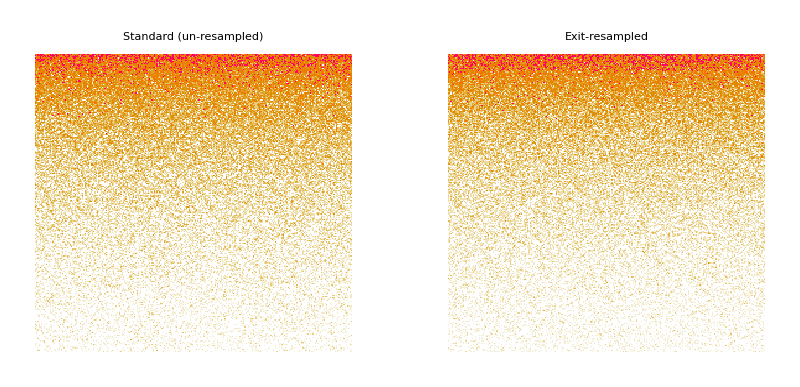

```mathematica
(*Assumes ePDFx,eCDFx,sampleExitDirX,PescClassical,PescDwivedi,PescMix are already defined above in this notebook (with the?NumericQ guards).*)

(*one standard (un-resampled) last-step escape contribution, at depth x-- returns 0 on any trial that doesn't happen to escape this step, exactly like a real walk would score it*)

standardContribution[x_?NumericQ,nu0_?NumericQ,gf_?NumericQ]:=Module[{guided,u,fwdPdfFactor,fwdStretch,sampleSigmaT,t,xNew,hit,tEff,pdfClassical,pdfDwivedi,pdfMix,trans,phaseLog},phaseLog=Log[(nu0+1)/(nu0-1)];
guided=RandomReal[]<gf;
u=If[guided,-(nu0-(nu0+1) Exp[-RandomReal[] phaseLog]),2 RandomReal[]-1];
fwdPdfFactor=1/((nu0+u) phaseLog);
fwdStretch=1+u/nu0;
sampleSigmaT=If[guided,fwdStretch,1];
t=-Log[1-RandomReal[]]/sampleSigmaT;
xNew=x+t*u;
hit=xNew<0&&u<-10^-9;
If[!hit,Return[0]];
tEff=-x/u;
pdfClassical=0.5 Exp[-tEff];
pdfDwivedi=fwdPdfFactor Exp[-fwdStretch tEff];
pdfMix=(1-gf) pdfClassical+gf pdfDwivedi;
trans=Exp[-tEff];
trans/pdfMix]

(*one resampled last-step contribution-- Pesc is precomputed OUTSIDE any per-pixel loop,since it's a real numeric integral and shouldn't be recomputed on every single trial*)
resampledContribution[x_?NumericQ,nu0_?NumericQ,gf_?NumericQ,Pesc_?NumericQ]:=Module[{uR,tR,transR,pdfR},If[RandomReal[]≥Pesc,Return[0]];
uR=sampleExitDirX[x];
tR=-x/uR;
transR=Exp[-tR];
pdfR=ePDFx[x,uR];
transR/(pdfR*Pesc)]

(*per-pixel:average*)
nTrialsPerPixel=8;
freq=256;
nu0Fixed=2.5;
gfFixed=0.75;
xMax=2.5;

(*depth swept across image width*)standardPanel[i_]:=Module[{x=(i/freq)*xMax},Mean[Table[standardContribution[x,nu0Fixed,gfFixed],{nTrialsPerPixel}]]]

resampledPanel[i_]:=Module[{x=(i/freq)*xMax,Pesc},Pesc=PescMix[x,nu0Fixed,gfFixed];
Mean[Table[resampledContribution[x,nu0Fixed,gfFixed,Pesc],{nTrialsPerPixel}]]]

standardData=ParallelTable[standardPanel[x],{x,freq},{y,freq}];
resampledData=ParallelTable[resampledPanel[x],{x,freq},{y,freq}];

GraphicsGrid[{{MatrixPlot[standardData,PlotRange->{0,1},ColorFunctionScaling->True,Frame->False,ImageSize->Medium,PlotLabel->"Standard (un-resampled)"],
MatrixPlot[resampledData,PlotRange->{0,1},ColorFunctionScaling->True,Frame->False,ImageSize->Medium,PlotLabel->"Exit-resampled"]}}]

(*ain't gonna work pretty well because we're using Mean and that averages out the stochastic noise across the pixel rows,and smooth 1D depth gradients hide variance differences extremely well.*)
```

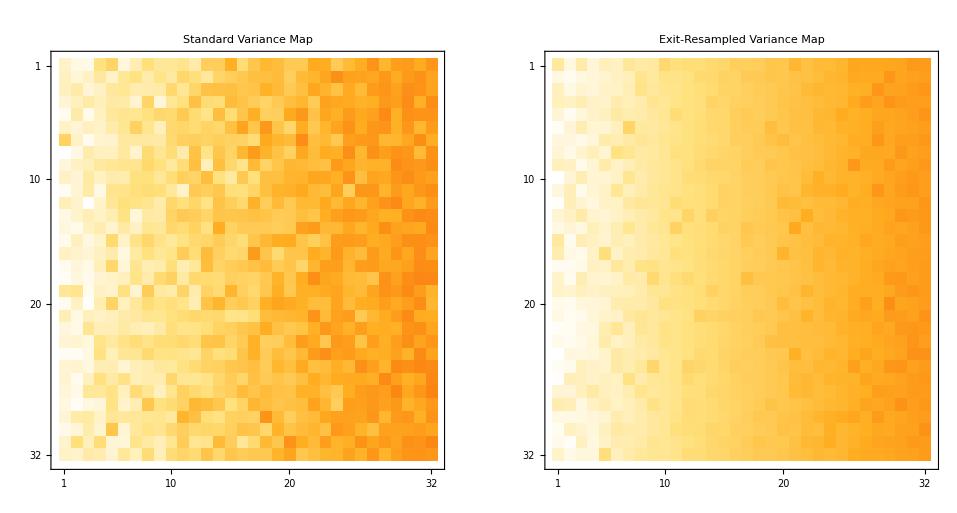

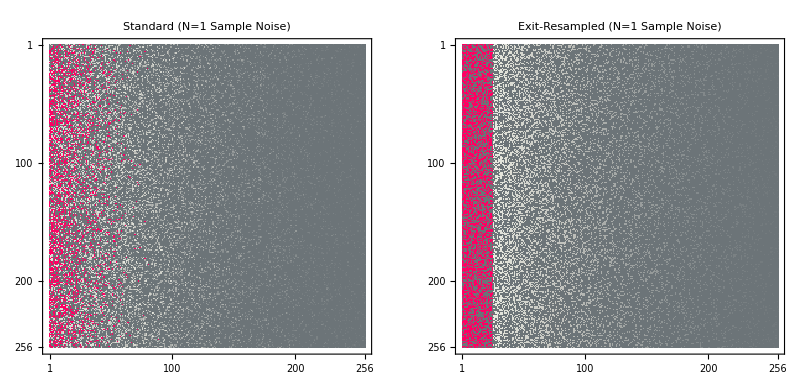

```mathematica
(*Monte Carlo Estimator Variance Benchmark*)

(*TOP: Standard deviation error map (N=64)| BOTTOM: Single-sample (N=1) noise output|Bottom:*)(*Note: Evaluates STD mapsand raw noise (N=1) directly instead of spatial means,*)

(*Settings to exaggerate noise differences*)
nTrialsPerPixel=1;

(*Single sample per pixel highlights estimator variance best*)
freq=256;
gfFixed=0.75;
xMax=3.5;

(*When $\nu_0$ approaches 1,the Dwivedi zero-variance directional distribution becomes significantly more forward-peaked,causing standard boundary sampling to suffer from massive weight spikes and high failure rates when attempting to escape*)
nu0Fixed=1.25;

(*Generate raw noisy single-sample estimates across the 2D grid*)
standardNoiseData=ParallelTable[standardContribution[(x/freq)*xMax,nu0Fixed,gfFixed],{y,freq},{x,freq}];

resampledNoiseData=ParallelTable[Module[{xVal=(x/freq)*xMax,Pesc},Pesc=PescMix[xVal,nu0Fixed,gfFixed];
resampledContribution[xVal,nu0Fixed,gfFixed,Pesc]],{y,freq},{x,freq}];

(*Compute Variance Maps over 64 trials per pixel to visualize noise reduction directly*)
nVarianceTrials=64;

standardVarData=ParallelTable[Variance[Table[standardContribution[(x/freq)*xMax,nu0Fixed,gfFixed],{nVarianceTrials}]],{y,32},{x,32}];

resampledVarData=ParallelTable[Module[{xVal=(x/freq)*xMax,Pesc},Pesc=PescMix[xVal,nu0Fixed,gfFixed];
Variance[Table[resampledContribution[xVal,nu0Fixed,gfFixed,Pesc],{nVarianceTrials}]]],{y,32},{x,32}];

(*Display Comparison*)
GraphicsGrid[{{MatrixPlot[standardVarData,ColorFunction->"SunsetColors",PlotLabel->"Standard Variance Map"],MatrixPlot[resampledVarData,ColorFunction->"SunsetColors",PlotLabel->"Exit-Resampled Variance Map"]}}]
GraphicsGrid[{{MatrixPlot[standardNoiseData,PlotRange->{0,1},ColorFunction->"GrayTones",PlotLabel->"Standard (N=1 Sample Noise)"],MatrixPlot[resampledNoiseData,PlotRange->{0,1},ColorFunction->"GrayTones",PlotLabel->"Exit-Resampled (N=1 Sample Noise)"]}}]
```

```mathematica
(*Assumes ePDFx,PescClassical,PescDwivedi,PescMix are defined above *)

(* Closed form -- exact, no integration needed*)
(* This is because the resampled direction sampler is EXACTLY zero-variance conditional on escape (verified: trans(u)/ePDFx(x,u) is constant in u,to 15+digits)*)(* Every bit of remaining variance comes from the Bernoulli escape gate alone.. does the ray escape or get absorbed/scattered*)

VarResampled[x_?NumericQ,nu0_?NumericQ,gf_?NumericQ]:=Module[{phaseLog,Pesc},phaseLog=Log[(nu0+1)/(nu0-1)];
Pesc=PescMix[x,nu0,gf];
ExpIntegralE[2,x]^2*(1-Pesc)/Pesc]

(*the standard scheme's variance,via direct integration over the escaping directions-- given u,the scored value on escape is deterministic,so only "which u, which branch, did it escape" is random;that lets mean and second moment reduce to plain 1D integrals over u instead of a full (branch,u,t) simulation*)

(*
VarStandard[x_?NumericQ,nu0_?NumericQ,gf_?NumericQ]:=Module[{phaseLog,pdfMixAtU,valueAtU,escProbClassical,escProbDwivedi,mean,second},phaseLog=Log[(nu0+1)/(nu0-1)];
pdfMixAtU[u_]:=Module[{tEff=-x/u,fwdStretch=1+u/nu0},(1-gf)*0.5*Exp[-tEff]+gf*(1/((nu0+u) phaseLog))*Exp[-fwdStretch tEff]];
valueAtU[u_]:=Exp[x/u]/pdfMixAtU[u];
escProbClassical[u_]:=Exp[x/u];
escProbDwivedi[u_]:=Exp[(1+u/nu0) x/u];
mean=NIntegrate[(1-gf)*0.5*escProbClassical[u]*valueAtU[u]+gf*(1/((nu0+u) phaseLog))*escProbDwivedi[u]*valueAtU[u],{u,-1,0},Method->"GaussKronrodRule"];
second=NIntegrate[(1-gf)*0.5*escProbClassical[u]*valueAtU[u]^2+gf*(1/((nu0+u) phaseLog))*escProbDwivedi[u]*valueAtU[u]^2,{u,-1,0},Method->"GaussKronrodRule"];
second-mean^2]

varianceRatio[x_?NumericQ,nu0_?NumericQ,gf_?NumericQ]:=VarStandard[x,nu0,gf]/VarResampled[x,nu0,gf]

gfFixed=0.75;
*)

(*Fast NIntegrate wrapper to prevent numerical slowdowns near nu0->1*)VarStandardFast[x_?NumericQ,nu0_?NumericQ,gf_?NumericQ]:=Module[{phaseLog,pdfMixAtU,valueAtU,escProbClassical,escProbDwivedi,mean,second},phaseLog=Log[(nu0+1)/(nu0-1)];
pdfMixAtU[u_]:=Module[{tEff=-x/u,fwdStretch=1+u/nu0},(1-gf)*0.5*Exp[-tEff]+gf*(1/((nu0+u) phaseLog))*Exp[-fwdStretch tEff]];
valueAtU[u_]:=Exp[x/u]/pdfMixAtU[u];
escProbClassical[u_]:=Exp[x/u];
escProbDwivedi[u_]:=Exp[(1+u/nu0) x/u];
mean=Quiet@NIntegrate[(1-gf)*0.5*escProbClassical[u]*valueAtU[u]+gf*(1/((nu0+u) phaseLog))*escProbDwivedi[u]*valueAtU[u],{u,-1,0},Method->"GaussKronrodRule",PrecisionGoal->3,MaxRecursion->10];
second=Quiet@NIntegrate[(1-gf)*0.5*escProbClassical[u]*valueAtU[u]^2+gf*(1/((nu0+u) phaseLog))*escProbDwivedi[u]*valueAtU[u]^2,{u,-1,0},Method->"GaussKronrodRule",PrecisionGoal->3,MaxRecursion->10];
Max[0,second-mean^2]]

(*Settings*)
gfFixed=0.75;
xRange={0.05,3.0};
nu0Range={1.15,5.0};
gridSize=35;

xGrid=Subdivide[xRange[[1]],xRange[[2]],gridSize];
nu0Grid=Subdivide[nu0Range[[1]],nu0Range[[2]],gridSize];

(*Fast parallel computation of 3D points {x,nu0,ratio}*)
ptsLinear=Flatten[ParallelTable[Module[{vStd=VarStandardFast[x,nu0,gfFixed],vRes=VarResampled[x,nu0,gfFixed]},{x,nu0,If[vRes>0,vStd/vRes,1.0]}],{nu0,nu0Grid},{x,xGrid}],1];

ptsLog=Map[{#[[1]],#[[2]],Log10[Max[1.0,#[[3]]]]}&,ptsLinear];

(*Smooth,continuous fast density plots*)
pLinear=ListDensityPlot[ptsLinear,ColorFunction->"TemperatureMap",PlotLegends->Automatic,InterpolationOrder->3,FrameLabel->{"x (optical depth)","ν0 (diffusion length)"},PlotLabel->"Linear: Var[standard] / Var[resampled]",ImageSize->Full];

pLog=ListDensityPlot[ptsLog,ColorFunction->"TemperatureMap",PlotLegends->Automatic,InterpolationOrder->3,FrameLabel->{"x (optical depth)","ν0 (diffusion length)"},PlotLabel->"Log10: Var[standard] / Var[resampled]",ImageSize->Full];

GraphicsRow[{pLinear,pLog},ImageSize->Full]

(*Top/Blue area ($\nu_0>3$):Near-isotropic regime where exit-resampling provides modest gains ($\sim 1\%\text{--}10\%$).*)
(*Bottom/Red boundary ($\nu_0\to 1$):Highly anisotropic regime where standard sampling breaks down*)


(*=================================================================================================================*)
(*Resolution of the 2D grid*)
xGrid=Subdivide[xRange[[1]],xRange[[2]],gridSize];
nu0Grid=Subdivide[nu0Range[[1]],nu0Range[[2]],gridSize];

(*Fast parallel computation over the 2D grid*)
dataLinear=ParallelTable[Module[{vStd=VarStandardFast[x,nu0,gfFixed],vRes=VarResampled[x,nu0,gfFixed]},If[vRes>0,vStd/vRes,1.0]],{nu0,Reverse[nu0Grid]},{x,xGrid}];

dataLog=Log10[Map[Max[1.0,#]&,dataLinear,{2}]];

(*Display side-by-side using full width*)
pLinear=MatrixPlot[dataLinear,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"Linear: Var[standard] / Var[resampled]",FrameTicks->{{Table[{i,nu0Grid[[gridSize-i+1]]},{i,1,gridSize,10}],None},{Table[{i,xGrid[[i]]},{i,1,gridSize,10}],None}},FrameLabel->{"x (optical depth)","ν0 (diffusion length)"},ImageSize->Full];

pLog=MatrixPlot[dataLog,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"Log10: Var[standard] / Var[resampled]",FrameTicks->{{Table[{i,nu0Grid[[gridSize-i+1]]},{i,1,gridSize,10}],None},{Table[{i,xGrid[[i]]},{i,1,gridSize,10}],None}},FrameLabel->{"x (optical depth)","ν0 (diffusion length)"},ImageSize->Full];

GraphicsRow[{pLinear,pLog},ImageSize->Full]
```

-Graphics-

-Graphics-